Your Title Here

```mathematica
L=5;d=2;r=0.5;
```

```mathematica
curved={
Line[{{-r,L+r},{-r,L+2*r},{d+r,L+2*r},{d+r,L+r}}],Line[{{-r,-r},{-r,-2*r},{d+r,-2*r},{d+r,-r}}],
Circle[{-r,L},r,{0,π/2}],Circle[{d+r,L},r,{π/2,π}],Circle[{-r,0},r,{3*π/2,2*π}],Circle[{d+r,0},r,{π,3*π/2}]};
```

```mathematica
bar1=Graphics[{Thick,curved,Line[{{#,0},{#,L}}]&/@{0,d}},ImageSize->{100,100}(*,Frame->True,FrameTicks->None*)];
```

```mathematica
bar2=Graphics[{Thick,curved,
BezierCurve[{{0,0},{0,0.1*L},{0.2*d,0.2*L}}],BezierCurve[{{d,0},{d,0.1*L},{0.8*d,0.2*L}}],
BezierCurve[{{0,L},{0,0.9*L},{0.2*d,0.8*L}}],BezierCurve[{{d,L},{d,0.9*L},{0.8*d,0.8*L}}],
Line[{{#*d,0.2*L},{#*d,0.8*L}}]&/@{0.2,0.8}
},ImageSize->{100,100}];
```

```mathematica
bar3=Graphics[{Thick,curved,
BezierCurve[{{0,0},{0,0.2*L},{0.3*d,0.3*L}}],BezierCurve[{{d,0},{d,0.2*L},{0.7*d,0.3*L}}],
BezierCurve[{{0,L},{0,0.8*L},{0.3*d,0.7*L}}],BezierCurve[{{d,L},{d,0.8*L},{0.7*d,0.7*L}}],
Line[{{#*d,0.3*L},{#*d,0.7*L}}]&/@{0.3,0.7}
},ImageSize->{100,100}];
```

```mathematica
bar4=Graphics[{Thick,curved,
BezierCurve[{{0,0},{0,0.3*L},{0.4*d,0.4*L}}],BezierCurve[{{d,0},{d,0.3*L},{0.6*d,0.4*L}}],
BezierCurve[{{0,L},{0,0.7*L},{0.4*d,0.6*L}}],BezierCurve[{{d,L},{d,0.7*L},{0.6*d,0.6*L}}],
Line[{{#*d,0.4*L},{#*d,0.6*L}}]&/@{0.4,0.6}
},ImageSize->{100,100}];
```

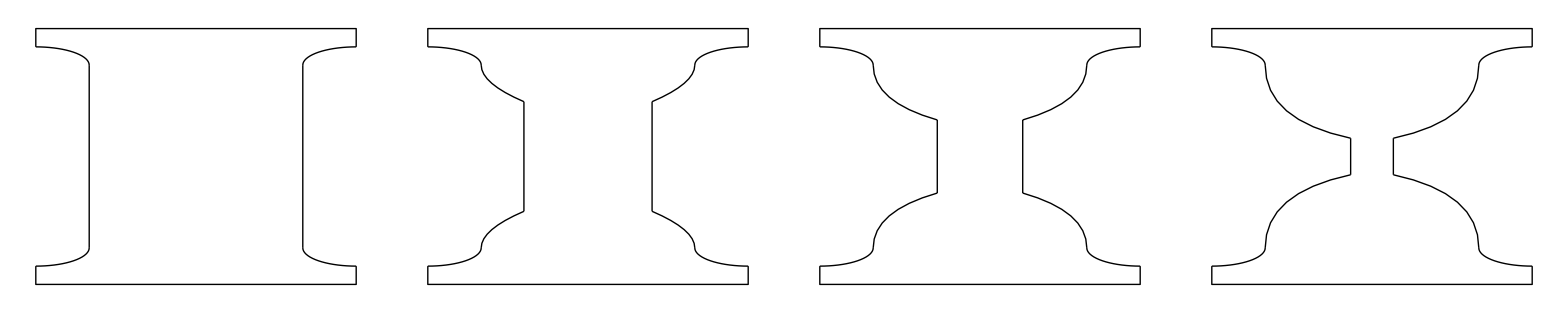

```mathematica
Grid@{{bar1,bar2,bar3,bar4}}
```





```mathematica
Manipulate[
Module[{ϵ},
ϵ[σ_]:=σ/e+k*(σ/e)^n;

Plot[ϵ[σ],{σ,0,0.1},PlotStyle->{Thick,Black},PlotRangePadding->{{Scaled@0.02,Scaled@0.02},{None,Scaled@0.02}},
Frame->True,FrameLabel->{Row@{"strain ",Style["ϵ",Italic]},Row@{"stress ",Style["σ",Italic]}},LabelStyle->{17,Black},ImageSize->{600,400},AspectRatio->Full,
Epilog->{
{PointSize@0.02,Point@{0.00015,ϵ[0.00015]},Point@{0.025,ϵ[0.025]},Point@{0.06,ϵ[0.06]},Point@{0.1,ϵ[0.1]}},
Mouseover[{Transparent,PointSize@0.04,Point@{0.00015,ϵ[0.00015]}},{Line[{{0.00015,ϵ[0.00015]},{0.02,ϵ[0.00015]}}],Inset[Framed[bar1,Background->White],{0.02,ϵ[0.00015]}]}],
Mouseover[{Transparent,PointSize@0.04,Point@{0.025,ϵ[0.025]}},{Line[{{0.025,ϵ[0.025]},{0.033,ϵ[0.0033]}}],Inset[Framed[bar2,Background->White],{0.033,ϵ[0.0033]}]}],
Mouseover[{Transparent,PointSize@0.04,Point@{0.06,ϵ[0.06]}},{Line[{{0.06,ϵ[0.06]},{0.06,ϵ[0.00323]}}],Inset[Framed[bar3,Background->White],{0.06,ϵ[0.00323]}]}],
Mouseover[{Transparent,PointSize@0.04,Point@{0.1,ϵ[0.1]}},{Line[{{0.1,ϵ[0.1]},{0.08,ϵ[0.004]}}],Inset[Framed[bar4,Background->White],{0.08,ϵ[0.004]}]}]
}]
],
Grid[{
{"material constants:",
Control[{{k,400,Style["K",Italic]},350,1100,10,Appearance->"Labeled",ImageSize->Small}],
Control[{{n,0.21,Style["n",Italic]},0.1,0.25,0.01,Appearance->"Labeled",ImageSize->Small}],
Text@Style[Row@{"ϵ",Style[" = ",FontSlant->Plain],"σ"/"E",Style[" + ",FontSlant->Plain],"K ",Superscript[""["σ"/"E"],"n"]},Italic,13]},
{Control[{{e,2000,"Young's modulus"},2000,9000,10,Appearance->"Labeled"}],SpanFromLeft}
},Alignment->Left]
]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX